# BTC-USD Moving Averages

```mathematica
Clear["Global`*"]
(* Buttons to hide / show code *)
CloseAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];SetOptions[#,CellOpen->False]&/@cells;];

OpenAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];SetOptions[#,CellOpen->True]&/@cells;];

Row[{Button["Hide Code",SelectionEvaluate[CloseAllInputsCells[]]],Button["Show Code",SelectionEvaluate[OpenAllInputsCells[]]]}]
```

Hide CodeShow Code

```mathematica
SetDirectory[NotebookDirectory[]];
(* Function shortcuts *)
st=StringTemplate;
dollar[a_]:=st["$``"][NumberForm[a,DigitBlock->3]];
(* Default properties for generated plots *)
imagesize=800;
imagemargins=20;
labelstyle=Directive[14];
titlestyle={20,Red};
subtitlestyle = {15};
imagemargins=20;
plotbackground=Lighter[LightGray,0.75];
updatedstr=Style[st["(updated: ``)"][DateString[]],subtitlestyle];

btcData=FinancialData[
"BTC/USD"
,"Jan 1 2012"
];
mo100=MovingAverage[btcData,100];
mo100latest=dollar[mo100["LastValue"]];
mo200=MovingAverage[btcData,200];
mo200latest=dollar[mo200["LastValue"]];
mo1yr=MovingAverage[btcData,365];
mo1yrlatest=dollar[mo1yr["LastValue"]];
mo2yr=MovingAverage[btcData,365*2];
mo2yrlatest=dollar[mo2yr["LastValue"]];
mo3yr=MovingAverage[btcData,365*3];
mo3yrlatest=dollar[mo3yr["LastValue"]];
mo4yr=MovingAverage[btcData,365*4];
mo4yrlatest=dollar[mo4yr["LastValue"]];
mo5yr=MovingAverage[btcData,365*5];
mo5yrlatest=dollar[mo5yr["LastValue"]];

plottypefunc=DateListPlot;
lines=Range[1];
selectlines=CheckboxBar[
Dynamic[lines]
,Map[Style[#,{16}]&,({1->"BTC",2->"100 day",3->"200 day",4->"1 year",5->"2 year", 6-> "3 year", 7-> "4 year", 8-> "5 year"}//Association)]//Normal
,Method->"Active"
];
plottype=1;
selectplottype=RadioButtonBar[
Dynamic[plottype]
,Map[Style[#,16]&,({1->"Linear",2->"Log"}//Association)]//Normal
,Method->"Active"
];
plotlines={
btcData
,mo100
,mo200
, mo1yr
, mo2yr
, mo3yr
, mo4yr
, mo5yr
};
plotlabels={"BTC"
,st["100 day mo: ``"][mo100latest]
,st["200 day mo: ``"][mo200latest]
,st["1 yr mo: ``"][mo1yrlatest]
,st["2 yr mo: ``"][mo2yrlatest]
,st["3 yr mo: ``"][mo3yrlatest]
,st["4 yr mo: ``"][mo4yrlatest]
,st["5 yr mo: ``"][mo5yrlatest]
};
plotlegends={"BTC (USD)"
,"100 Day MA"
,"200 Day MA"
,"1 Year MA"
,"2 Year MA"
,"3 Year MA"
,"4 Year MA"
,"5 Year MA"
};
```

```mathematica
Manipulate[
Module[
{plotlabel, plottypefunc}
,plotlabel=Column[
Join[{
Style["Bitcoin Price (USD)" ,titlestyle]
,Style["Latest: $"  <> ToString[NumberForm[btcData["LastValue"],DigitBlock->3]],subtitlestyle]
}
,Style[#,subtitlestyle]&/@Part[
plotlabels
,Select[lines,#!=1&]
]
]
,Center
];
plottypefunc:=If[plottype==1,DateListPlot,DateListLogPlot];
plottypefunc[
Part[
plotlines
,lines
]
,ImageSize->imagesize
,ImageMargins->imagemargins
,PlotRange->Full
,GridLines->{DateRange[{2012},{2027},"Year"],Automatic}
,FrameTicks->All
,PlotLabel->Column[
{
plotlabel
,updatedstr
}
,Center]
,PlotLegends->Part[
plotlegends
,lines
]
]
]
,Dynamic[selectlines]
,Dynamic[selectplottype]
]
```

## Past n days moving average

```mathematica
Manipulate[
Module[
{btcn, mon, meann,mean}
,btcn=Take[btcData//Normal,-n];
mon= Take[MovingAverage[btcData,n]//Normal,-n];
(*mon= MovingAverage[btcData,n]//Normal;*)
mean=Mean[Last /@btcn];
meann=NumberForm[Mean[Last /@btcn],DigitBlock->3];
plotlabel = Column[{
Style["Bitcoin Price (USD)" ,titlestyle]
,Style["Latest: $"  <> ToString[NumberForm[btcData["LastValue"],DigitBlock->3]] ,subtitlestyle]
,Style["Current " <> ToString[n]<>" Day Moving Average: "<>dollar[meann],subtitlestyle]
,updatedstr
}
,Center
];
Column[{
DateListPlot[
{btcn, mon}
,PlotLabel->plotlabel
,PlotLegends->{
"Price"
,ToString[n] <> " Day Moving Average"
}
,PlotRange->Full
,ImageSize->1000
,GridLines->{
Automatic
,Join[{{mean,Directive[{Red,Thick, Dashed}]}},Range[0,200000,5000]]
}
,FrameTicks->All
]
,Spacer[20]
,DateListPlot[
{First[#]//First,N[((First[#]//Last)-(Last[#]//Last))/(First[#]//Last)]}&/@ MapThread[List,{btcn,mon}]
,PlotLabel->Column[{
Style["Relative above/below the moving average",titlestyle]
,updatedstr
}
,Center
]
,ImageSize->1000
,GridLines->{Automatic, Join[Range[-10,10,0.05],{{0,Thick}}]}
,FrameTicks->All
]
}]
]
,{{n,200,Style["Moving Average",16]},Join[{100-> "100 days",200 -> "200 days",500-> "500 days"},MapIndexed[#1 -> ToString[First[#2]] <> " yr"&,Range[365,365 * 6,365]]]//Sort}
]
```

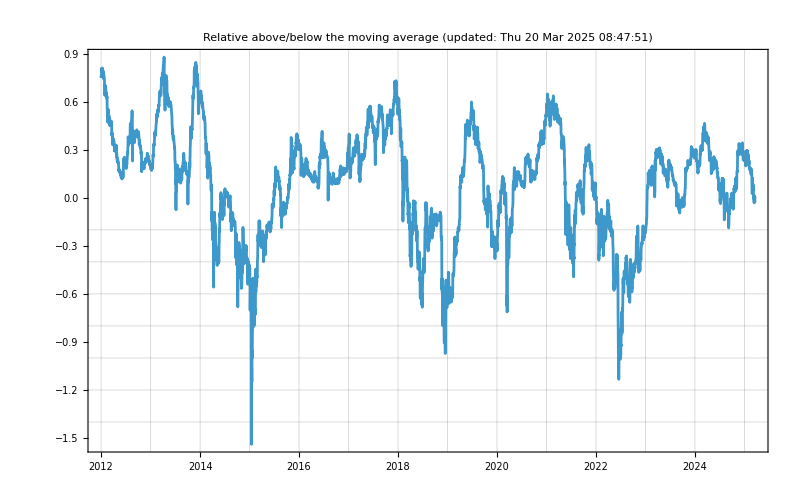

```mathematica
int1=TimeSeriesThread[(#[[1]]-#[[2]])/(#[[1]])&,{plotlines[[1]],plotlines[[3]]},ResamplingMethod->{"Interpolation",InterpolationOrder->1}];
DateListPlot[
int1
,PlotLabel->Column[{
Style["Relative above/below the moving average",titlestyle]
,updatedstr
}
,Center
]
,GridLines->{DateRange[{2012},{2027},"Year"],Join[Range[-10,10,0.2],{#,Thick}&/@Range[-10,10]]}
,FrameTicks->All
,ImageSize->imagesize
]
```